A question about an info graphic in American Scientist summer 2025, very effectively displaying the connections across some partition. Connections closer by were visible at the base but grew thinner at their apex, some ways in. Connections further across are wider all the way.

We guess these are parabolas meeting the unit circle at right angles. With a vertical axis, they are thus
y == a x^2 + b 
Points (x0,y0) at the intersection satisfy that and
x^2 + y^2 = 1.  
 They have tangents
 (1,2a x0) and (-y0,x0); these are perpendicular. Hence  a= y0/2x0^2 and the equation is 
 y = y0/2x0^2 x^2 + b.  We find be as b = y0 – a x0^2 = y0 - y0/2 = y0/2 (!)
 
Taking x0, y0 = cos,sin = c,s we have
y = s/2 (c^2 x^2 +1)

Reparametrizing (so that the parabolas begin and end on the unit circle) this simplifies even further to 

x= c t
y = s/2 (t^2+1)

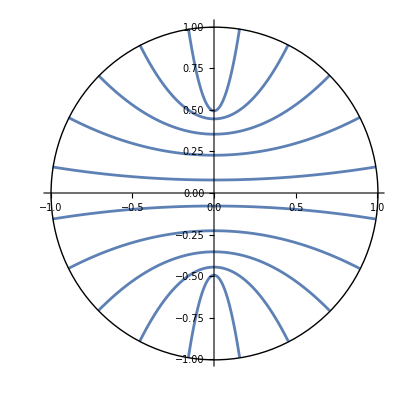

```mathematica
With[{num=5},
Show[
ParametricPlot[Table[{t Cos[θ],Sin[θ]/2(t^2+1)},{θ,-Pi/2+Pi/(4num),Pi/2-Pi/(4num),Pi/(2num)}],{t,-1,1}],
Graphics[{Circle[{0,0},1]}],
PlotRange->{{-1,1},{-1,1}}
]]
```

This looks about like it

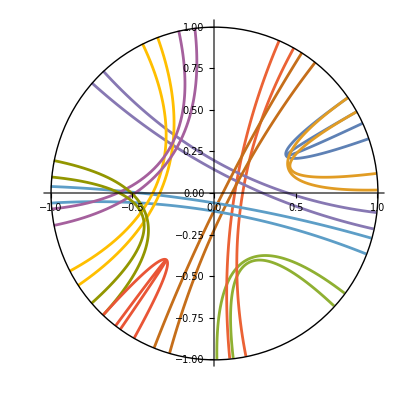

```mathematica
With[{num=20,threshold=.015},functions = (Join@@Table[If[Random[]<threshold,
Join@@(Table[{t Cos[θ+δ],Sin[θ+δ]/2(t^2+1)},{δ,0,.1,.1}].{{Cos[ρ],Sin[ρ]},{-Sin[ρ],Cos[ρ]}}),"X"]
,{θ,-Pi/2+Pi/(4num),Pi/2-Pi/(4num),Pi/(2num)},{ρ,0,Pi-Pi/num,Pi/num}])//Select[#,!(#==="X")&]&;
Show[
ParametricPlot[functions,{t,-1,1}],
Graphics[{Circle[{0,0},1]}],
PlotRange->{{-1,1},{-1,1}}
]]
```

The same thing with catenaries:

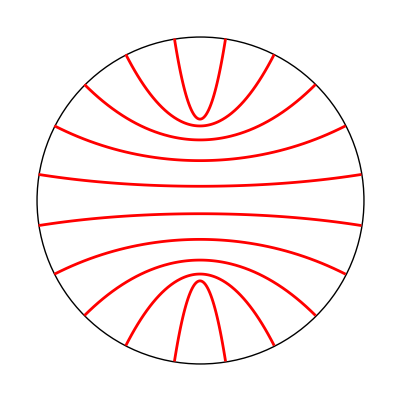

```mathematica
With[{num=5},Show[Graphics[{Circle[{0,0},1]}],
Table[x0=Cos[δ];y0=Sin[δ];ParametricPlot[{t,y0/x0/Sinh[x0]Cosh[t]+y0(1-Coth[x0]/x0)},{t,-Cos[δ],Cos[δ]},PlotStyle->Red],
{δ,-Pi/2+Pi/(4num),Pi/2-Pi/(4num),Pi/(2num)}]]]
```

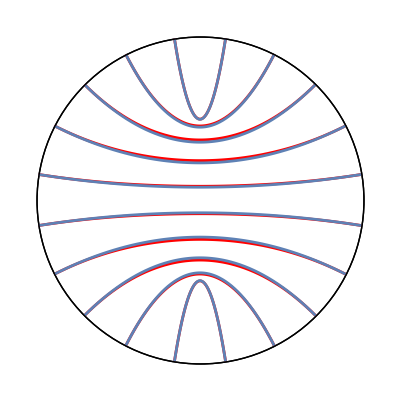

```mathematica
Show[%109,%110]
```

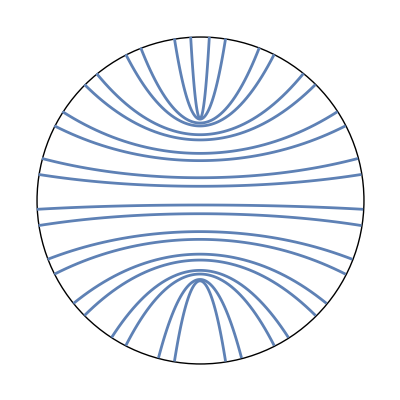

```mathematica
With[{num=5},Show[Graphics[{Circle[{0,0},1]}],
Table[x0=Cos[δ+ω];y0=Sin[δ+ω];ParametricPlot[{t,y0/x0/Sinh[x0]Cosh[t]+y0(1-Coth[x0]/x0)},{t,-Cos[δ+ω],Cos[δ+ω]}],
{δ,-Pi/2+Pi/(4num),Pi/2-Pi/(4num),Pi/(2num)},{ω,0,.1,.1}]]]
```

```mathematica
With[{num=20,threshold=.015},functions = (Join@@Table[If[Random[]<threshold,
Join@@(Table[{t Cos[θ+δ],Sin[θ+δ]/2(t^2+1)},{δ,0,.1,.1}].{{Cos[ρ],Sin[ρ]},{-Sin[ρ],Cos[ρ]}}),"X"]
,{θ,-Pi/2+Pi/(4num),Pi/2-Pi/(4num),Pi/(2num)},{ρ,0,Pi-Pi/num,Pi/num}])//Select[#,!(#==="X")&]&;
Show[
ParametricPlot[functions,{t,-1,1}],
Graphics[{Circle[{0,0},1]}],
PlotRange->{{-1,1},{-1,1}}
]]
```

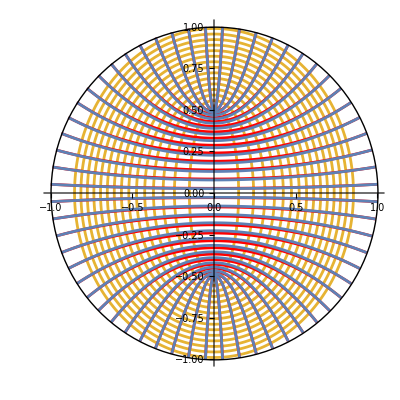

```mathematica
With[{num=15},
Show[
Table[
ParametricPlot[{√(a^2-1/4)Cos[t],a Sin[t]},{t,0,2Pi},PlotStyle->RGBColor[.9,.7,.2]],{a,1/2+1/3/num,1,1/2/(num)}],
Table[x0=Cos[δ];y0=Sin[δ];
ParametricPlot[{t,y0/x0/Sinh[x0]Cosh[t]+y0(1-Coth[x0]/x0)},{t,-Cos[δ],Cos[δ]},PlotStyle->Red],
{δ,-Pi/2+Pi/(4num),Pi/2-Pi/(4num),Pi/(2num)}],
ParametricPlot[Table[{t Cos[θ],Sin[θ]/2(t^2+1)},{θ,-Pi/2+Pi/(4num),Pi/2-Pi/(4num),Pi/(2num)}],{t,-1,1}],
Graphics[{Circle[{0,0},1]}],
PlotRange->{{-1,1},{-1,1}}
]]
```